Claw Game - Project 7
Jacob Schnoor

Visualization of Prize Locations

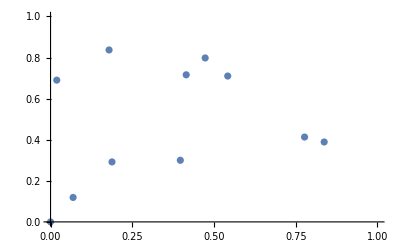

Position begins at (0,0)

These are the Ordered Pairs for Instructions

The following represent (c_u,c_v) such that

position_previous+c_uu+c_vv=position_prize

(2.18494 | -0.231966
0.724376 | -0.498558
-2.04001 | 0.664065
-0.391656 | 0.858048
1.94537 | -1.03441
-1.76637 | 0.480418
1.89085 | -1.03273
-0.532234 | 0.760897
-1.37863 | 0.707147
-0.273523 | -0.711422)

Result of Using Instructions

{0,0}

{0.415,0.716}

{0.179,0.837}

{0.188,0.292}

{0.837,0.389}

{0.473,0.798}

{0.397,0.3}

{0.019,0.69}

{0.542,0.71}

{0.777,0.413}

{0.069,0.119}

```mathematica
u={0.284,0.357};
v={0.886,0.276};
prizes = {{0,0},{0.415,0.716},{0.179,0.837},{0.188,0.292},{0.837,0.389},{0.473,0.798},{0.397,0.300},{0.019,0.690},{0.542,0.710},{0.777,0.413},{0.069,0.119}};
Print["\n\nVisualization of Prize Locations"];
ListPlot[prizes,PlotRange->{{0,1},{0,1}}]
basisMat={{u[[1]],v[[1]]},{u[[2]],v[[2]]}};
instructions=Table[0,{m,10},{n,2}];
For[i=2, i≤11,i++,
instructions[[i-1]]=LinearSolve[basisMat,{prizes[[i,1]]-prizes[[i-1,1]],prizes[[i,2]]-prizes[[i-1,2]]}];
];
Print["\n\nPosition begins at (0,0)"];
Print["These are the Ordered Pairs for Instructions"];
Print["The following represent (c_u,c_v) such that"];
Print["position_previous+c_uu+c_vv=position_prize"];
instructions//MatrixForm
Print["\n\nResult of Using Instructions"];
position={0,0}
For[i=1, i≤10, i++,
position+=instructions[[i,1]]*u;
position+=instructions[[i,2]]*v;
Print[position]
];
```

Explanation:
	To create the ordered pair of numbers (c_u,c_v) such that position_previous+c_u u+c_v v=position_prize, one can think of the problem as a system of equations. To start off, we need to go from (0,0) to (0.415,0.716) using a linear combination of the vectors u and v. That means that something times u plus something times v must give us the first prize position.
In numbers, that looks like:
	c_u(0.284
0.357)+c_v(0.886
0.276)=(0.415
0.716)
or
	Piecewise[{{0.284 c_u+0.886 c_v=, 0.415}, {0.357 c_u+0.276 c_v=, 0.716}}]	
Which can be unified into one matrix like so:
	(0.284 | 0.886 | |     0.415
0.357 | 0.276 | |     0.716)
Using LinearSolve in Mathematica, we find out that the solution to this matrix is:
	c_u=2.18494
	c_v=-0.231966
For the next position, we must recognize that we’re no longer at the origin. We must factor in the current position to help us get to the next one. If we assume we did the last step correctly, then that means we’re currently at (0.415,0.716) and we’re trying to get to (0.179,0.837). Again we use the same vectors for u and v and solve for the scalar variables, c.
	(0.415
0.716)+c_u(0.284
0.357)+c_v(0.886
0.276)=(0.179
0.837)
	
	c_u(0.284
0.357)+c_v(0.886
0.276)=(0.179
0.837)-(0.415
0.716)
	
	Piecewise[{{0.284 c_u+0.886 c_v=, 0.179-0.415}, {0.357 c_u+0.276 c_v=, 0.837-0.716}}]
	
	Piecewise[{{0.284 c_u+0.886 c_v=, -.236}, {0.357 c_u+0.276 c_v=, .121}}]
	
	(0.284 | 0.886 | |     -.236
0.357 | 0.276 | |        .121)
	
	 c_u=0.724376
	c_v=-0.498558
To find all the next ordered pairs, it’s simply a matter of setting the matrix composed of u and v equal to the RELATIVE position of the next point. (For example if x1=5 and x2=8, then the relative position of x2 is 8-5 or 3 units in the positive direction)
For all positions n>1, solve the matrix:

	(u | v | =   x_n-x_(n-1)
| | | | =   y_n  -y_(n-1))
Using a for loop along with the LinearSolve method, all these ordered pairs may be stored in a matrix of their own labeled “instructions” as seen in the code above